First, run ResourceFunction["MaTeXInstall"][] to install MaTeX

```mathematica
<<MaTeX`
```

```mathematica
Tc=1;
```

```mathematica
dF[x_,f0_]:=Piecewise[{{-f0(x-Tc)^2/Tc^2,x<Tc},{0,x>Tc}}]
```

```mathematica
(**From numerics, α increases almost linearly with temperature**)
```

```mathematica
α[x_,α0_]:=Piecewise[{{1-(1-α0)((Abs[x-Tc])^2/Tc^2),x<Tc},{1,x>Tc}}]
```

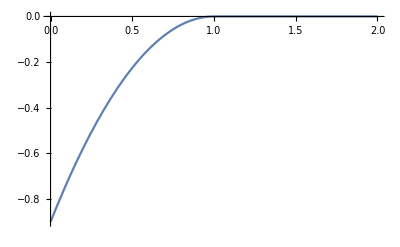

```mathematica
Plot[dF[x,0.9],{x,0,2Tc},PlotRange->All]
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->30};
```

```mathematica
legend=SwatchLegend[{Green,Blue,Orange},{MaTeX["\\alpha_0 = 0.95",Magnification->2.2],MaTeX["\\alpha_0 = 0.9",Magnification->2.2],MaTeX["\\alpha_0 = 0.8",Magnification->2.2]},LegendMarkers->{Graphics[{Line[{{-1,0},{1,0}}]}]},LegendMarkerSize->25];
```

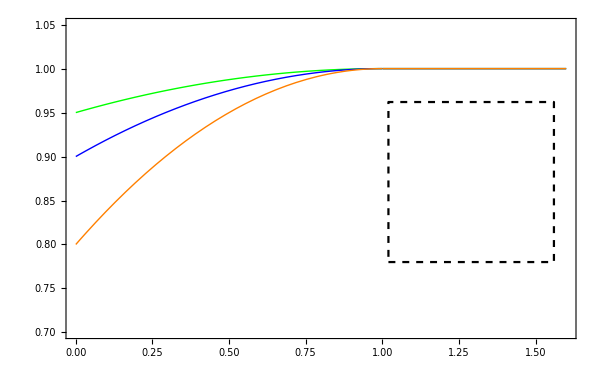

```mathematica
Legended[Show[Plot[α[x Tc,0.95],{x,0,1.6},PlotRange->{All,{0.7,1.05}},PlotStyle->{Green,Thick}],Plot[α[x Tc,0.9],{x,0,1.6},PlotRange->{All,{0.7,1.05}},PlotStyle->{Blue,Thick}],Plot[α[x Tc,0.8],{x,0,1.6},PlotRange->{All,{0.7,1.05}},PlotStyle->{Orange,Thick}],
ListPlot[{{1.02,0.78},{1.56,0.78},{1.56,0.962},{1.02,0.962},{1.02,0.78}},Joined-> True,PlotStyle-> {Black,Dashed}],
Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2.5],MaTeX["\\alpha(T)",Magnification->2.5]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,RotateLabel-> False,ImageSize->600],
Placed[legend,Scaled[{0.8,0.5}]]]
```

```mathematica
curvAvg[x_,α0_,f0_]:=(1+Exp[-dF[x,f0]/x])/(1 + α[x,α0]Exp[-dF[x,f0]/x])
```

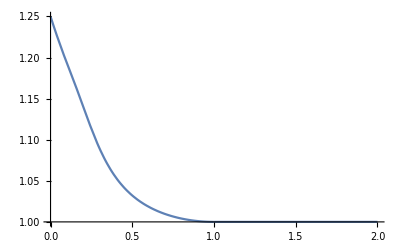

```mathematica
Plot[curvAvg[x,0.8,1],{x,0,2Tc},PlotRange->All]
```

```mathematica
w0 = 1;
```

```mathematica
wTBG=0.1;
```

```mathematica
(**Bloch-Gruneisen model**)
```

```mathematica
TBG=0.8Tc
```

0.8

```mathematica
(** scatteringFreqWithoutDomainTBG[x_]:=Piecewise[{{w0,x<=TBG},{w0+wTBG(x-TBG)/TBG,x>TBG}}] **)
```

```mathematica
scatteringFreqWithoutDomainTBG[x_]:=w0 + wTBG(Sqrt[Sqrt[1+(x/TBG)^4]]-1)
```

```mathematica
(**Plots for f0/kBT = 1**)
```

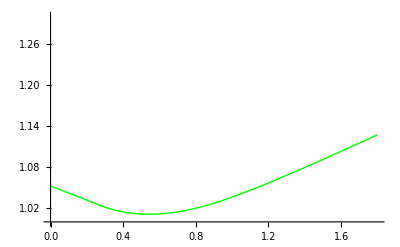

```mathematica
p1=Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.95,1],{x,0,1.8},PlotStyle->{Green,Thick},PlotRange->{All,{1.0,1.3}}]
```

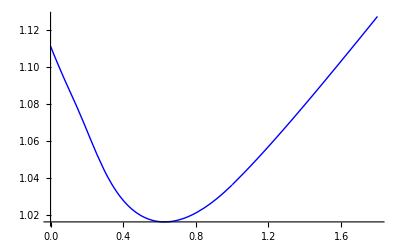

```mathematica
p2=Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.9,1],{x,0,1.8},PlotStyle->{Blue,Thick},PlotRange->All]
```

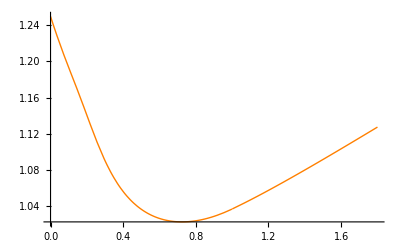

```mathematica
p3=Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.8,1],{x,0,1.8},PlotStyle->{Orange,Thick},PlotRange->All]
```

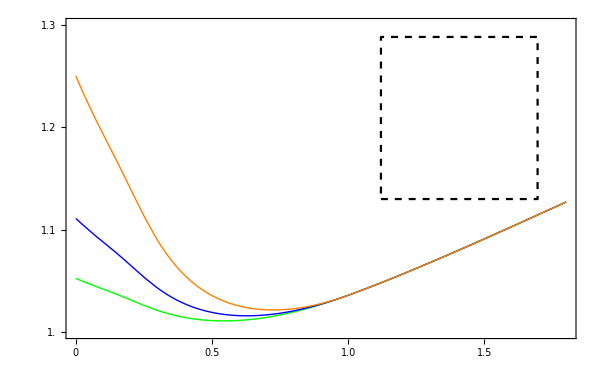

```mathematica
Legended[Show[p1,p2,p3,
ListPlot[{{1.12,1.13},{1.695,1.13},{1.695,1.288},{1.12,1.288},{1.12,1.13}},Joined-> True,PlotStyle-> {Black,Dashed}],FrameTicks-> {{{1.0,1.1,1.2,1.3},None},{{0,0.5,{1.0,"1.0"},1.5},None}},Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2.5],MaTeX["\\frac{\\rho_{xx}}{\\rho_\\text{Min}}",Magnification->2.5]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600],
Placed[legend,Scaled[{0.775,0.7}]]]
```

```mathematica
(**Plots for f0/kBT_c = 1000 **)
```

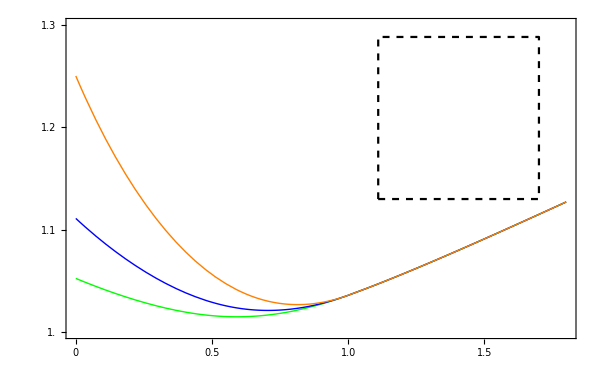

```mathematica
Legended[Show[Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.95,1000],{x,0,1.8},PlotStyle->{Green,Thick},PlotRange->{All,{1.0,1.3}},
PlotLabel->MaTeX["\\frac{F_0}{k_B T_c}=10^{3}",Magnification->2.4]],
Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.9,1000],{x,0,1.8},PlotStyle->{Blue,Thick},PlotRange->{All,{1.0,1.3}}],
Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.8,1000],{x,0,1.8},PlotStyle->{Orange,Thick},PlotRange->{All,{1.0,1.3}}],
ListPlot[{{1.11,1.13},{1.7,1.13},{1.7,1.288},{1.11,1.288},{1.11,1.13}},Joined-> True,PlotStyle-> {Black,Dashed}],FrameTicks-> {{{1.0,1.1,1.2,1.3},None},{{0,0.5,{1.0,"1.0"},1.5},None}},Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2.5],MaTeX["\\frac{\\rho_{xx}}{\\rho_\\text{Min}}",Magnification->2.5]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600],
Placed[legend,Scaled[{0.775,0.7}]]]
```

```mathematica
(**Plots for f0/kBT_c = 1/1000 **)
```

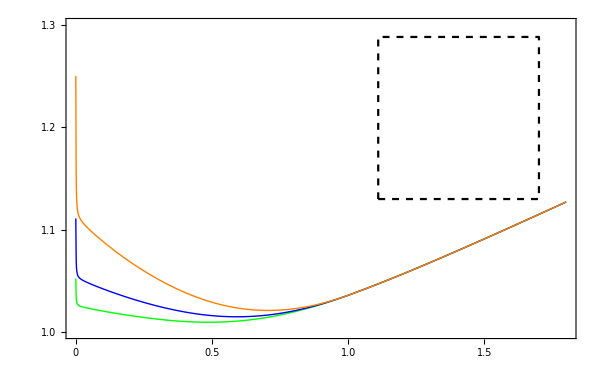

```mathematica
Legended[Show[Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.95,1/1000],{x,0,1.8},PlotStyle->{Green,Thick},PlotRange->{All,{1.0,1.3}},PlotLabel->MaTeX["\\frac{F_0}{k_B T_c}=10^{-3}",Magnification->2.4]],
Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.9,1/1000],{x,0,1.8},PlotStyle->{Blue,Thick},PlotRange->{All,{1.0,1.3}}],
Plot[scatteringFreqWithoutDomainTBG[x Tc]curvAvg[x Tc,0.8,1/1000],{x,0,1.8},PlotStyle->{Orange,Thick},PlotRange->{All,{1.0,1.3}}],
ListPlot[{{1.11,1.13},{1.7,1.13},{1.7,1.288},{1.11,1.288},{1.11,1.13}},Joined-> True,PlotStyle-> {Black,Dashed}],FrameTicks-> {{{{1.0,"1.0"},1.1,1.2,1.3},None},{{0,0.5,{1.0,"1.0"},1.5},None}},Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2.5],MaTeX["\\frac{\\rho_{xx}}{\\rho_\\text{Min}}",Magnification->2.5]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600],
Placed[legend,Scaled[{0.775,0.7}]]]
```

```mathematica
(**Plots for Ground state vs two-fluid model **)
```

```mathematica
legend2=SwatchLegend[{Red,Blue},{MaTeX["\\text{Two Fluid}",Magnification->2],MaTeX["\\text{Ground State}",Magnification->2]},LegendMarkers->{Graphics[{Line[{{-1,0},{1,0}}]}]},LegendMarkerSize->25];
```

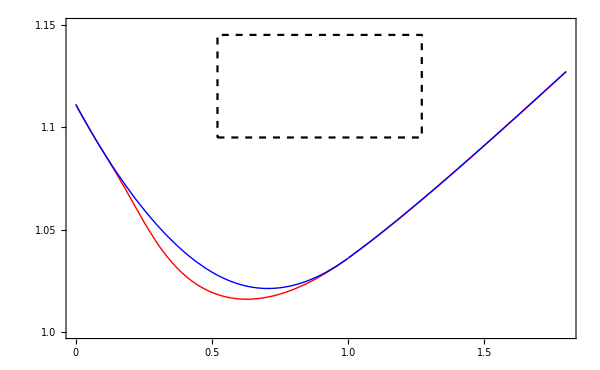

```mathematica
Legended[Show[Plot[scatteringFreqWithoutDomainTBG[x Tc]*curvAvg[x Tc,0.9,1],{x,0,1.8},PlotStyle->{Red,Thick},PlotRange->{All,{1.0,1.15}}],
Plot[scatteringFreqWithoutDomainTBG[x Tc]*(1/α[x,0.9]),{x,0,1.8},PlotStyle->{Blue,Thick},PlotRange->{All,{1.0,1.3}}],
ListPlot[{{0.52,1.095},{1.27,1.095},{1.27,1.145},{0.52,1.145},{0.52,1.095}},Joined-> True,PlotStyle-> {Black,Dashed}],FrameTicks-> {{{{1.0,"1.0"},1.05,1.1,1.15},None},{{0,0.5,{1.0,"1.0"},1.5},None}},Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2.5],MaTeX["\\frac{\\rho_{xx}}{\\rho_\\text{Min}}",Magnification->2.5]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600],
Placed[legend2,Scaled[{0.5,0.8}]]]
```